# M. sexta - D. discolor Eco-Evolutionary Model

```mathematica
Clear["Global`*"]
```

### Ecological dynamics (Eqs. 9)

{P→1.49854,L→0.678235,A→0.0284859}

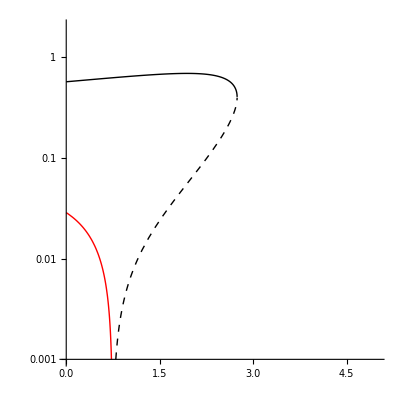

```mathematica
(* Coevolved ecological parameters (Supplementary Tables 1,2): subscripts dropped for convenience *)
param={b->3.6,v->7,H->0.1,m->0.003,ϵ->1,e->0.7,dL->0.3,dA->0.2};

(* Ecological dynamics *)
dPdt=P(1-P)+((b v A)/(H+v A))P-h L P;
dLdt=ϵ e v P A-m h L-dL L;
dAdt=m h L-dA A;

(* Equilibria *)
eq=Simplify[Solve[{dPdt==0,dLdt==0,dAdt==0},{P,L,A}]];

(* Coexistence equilibrium *)
ecoCoex=eq[[3]];
ecoCoex/.param/.h->2.8


(* Supplementary Figure 1: Bifurcation diagram of larval density *)
s1b=LogPlot[{ecoCoex[[2,2]]/.b->0/.param/.h->5-x,eq[[2,2,2]]/.param/.h->5-x,ecoCoex[[2,2]]/.param/.h->5-x},{x,0,5},PlotRange->{{0,5},{0.001,2}},AspectRatio->1,PlotStyle->{{Red,Thick},{Black,Dashed,Thick},{Black,Thick}},TicksStyle->Black,Ticks->{Automatic,{0.001,0.01,0.1,1}},AxesStyle->Black,LabelStyle->Directive[FontSize->20]]
```

### Coevolutionary dynamics (Eqs. 10-11)

#### Resident ancestral interaction (Eq. 10)

```mathematica
(* Parameters: subscripts dropped for convenience *)
param={vMax->50,hMax->5,bMax->5,eMax->1,vP->0,vI->0,hP->0,hI->0,bP->0,H->0.1,m->0.003,ϵ->1,dL->0.3,dA->0.2,vS->1,hS->1,bS->1,cIV->0.5,cIH->0.5};

(* Ecological dynamics *)
Clear[vf,hf,bf,ef]
dPdt=P(1-P)+((bf vf A)/(H+vf A))P-hf L P;
dLdt=ϵ ef vf P A-m hf L-dL L;
dAdt=m hf L-dA A;

(* Equilibria *)
eq=Simplify[Solve[{dPdt==0,dLdt==0,dAdt==0},{P,L,A}]];

(* Trait functions *)
(* Note: vP, hP, bP, hI, vI used instead of x_i and y_i as in manuscript *)
(* Note: vS, hS, bS used instead of V_i', H_i', R_i' as in manuscript *)
(* Note: cIH, cIV used instead of c^x_I,i as in manuscript *)
vf=vMax/(1+Exp[-vS(vP+vI)]);
hf=hMax/(1+Exp[hS(hP-hI)]);
bf=bMax(2/(1+Exp[-bS bP])-1);
ef=eMax Exp[-(cIH hI^2+cIV vI^2)];

(* Coexistence equilibrium *)
coex=eq[[3]];
coex/.param
```

{P→0.328,L→0.2688,A→0.01008}

#### Invasion fitness and selection gradients (Eqs. 11)

```mathematica
(* Mutant insect trait functions *)
Clear[vfMut,hfMut,efMut]
vfMut=vMax/(1+Exp[-vS(vP+vImut)]);
hfMut=hMax/(1+Exp[hS(hP-hImut)]);
efMut=Exp[-(cIH hImut^2+cIV vImut^2)];

(* Invasion fitness *)
(* Plant *)
Wp=(1-(1+cB (bPmut-bP)+cPV (vPmut-vP)+cPH(hPmut-hP))P)+((bMax(2/(1+Exp[-bS bPmut])-1)(vMax/(1+Exp[-vS(vPmut+vI)])) A)/(H+(vMax/(1+Exp[-vS(vPmut+vI)])) A))-(hMax/(1+Exp[hS(hPmut-hI)])) L;
(* Insect *)
Wi=1/2 (-dA-dL-hfMut m+√((dA+dL+hfMut m)^2-4 (dA dL+dA hfMut m-(dA hfMut (dL+hf m) efMut vfMut)/(hf ef vf))));

(* Selection Gradients *)
(* Plant *)
dRdt=D[Wp,bPmut]/.coex/.bPmut->bP/.vPmut->vP/.hPmut->hP;
dHPdt=D[Wp,hPmut]/.coex/.bPmut->bP/.vPmut->vP/.hPmut->hP;
dVPdt=D[Wp,vPmut]/.coex/.bPmut->bP/.vPmut->vP/.hPmut->hP;
(* Insect *)
dHIdt=D[Wi,hImut]/.vImut->vI/.hImut->hI;
dVIdt=D[Wi,vImut]/.vImut->vI/.hImut->hI;
```

#### Simulate evolutionary dynamics

##### Note: The error “NDSolve: The function value ... is not a real number when the arguments are ... ” indicates evolutionary purging of the insect. The error occurs because the insect equilibrium becomes an imaginary number when it is extinct. To avoid evolutionary purging, try varying the value of cPV and/or cPH or increasing vMax Note: If host evolves zero defense, try increasing hMax Note: for the ancestral interaction, set bMax = 0, cB = 0, and cPV = 0

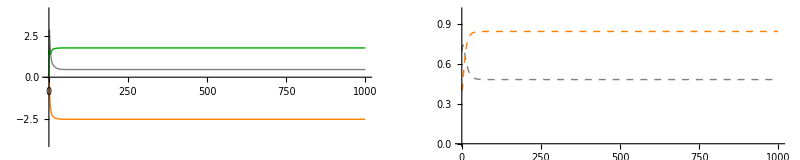

hP: 0.460159 vP: -2.5283 bP: 1.75974

hI: 0.48228 vI: 0.843534

v: 7.82328 h: 2.52765 b: 3.53177

e: 0.623709 Equilibrium: {P→1.66258,L→0.665115,A→0.0252177}

```mathematica
(* Parameters *)
(* Note: cB, cPH, cPV used instead of c^x_P,i as in manuscript *)
evoParam={vMax->50,hMax->5,bMax->5,eMax->1,H->0.1,ϵ->1,m->0.003,dL->0.3,dA->0.2,bS->1,vS->1,hS->1,cB->0.5,cPV->0.4,cPH->0.5,cIV->0.5,cIH->0.5};
end=1000; (* how long to run eco-evolutionary model *)

(* Evolutionary dynamics *)
Off[NDSolve::nrnum1]
Off[NDSolve::evcvmit]
Off[InterpolatingFunction::dmval]
dHPt=hP'[T]==-(cPH dA ⅇ^(cIH hI[T]^2+cIV vI[T]^2) (1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)) (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS))))/(hMax m vMax ϵ)+1/(2 hMax m vMax^2 ϵ)ⅇ^(cIH hI[T]^2+(-hI[T]+hP[T]) hS+cIV vI[T]^2) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2 hS (-(dA dL vMax)/(1+ⅇ^(-(vI[T]+vP[T]) vS))-(dA hMax m vMax)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-(dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) (-1+2/(1+ⅇ^(-bP[T] bS))) hMax m bMax vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+√(1/((1+ⅇ^(-(vI[T]+vP[T]) vS))^2)vMax^2 (-1/(1+ⅇ^((-hI[T]+hP[T]) hS))4 dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax ϵ (dA (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS)))-(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))))+((ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m (1+(-1+2/(1+ⅇ^(-bP[T] bS))) bMax) vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-dA (dL+(hMax (m+ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H ϵ))/(1+ⅇ^((-hI[T]+hP[T]) hS))))^2)));
dVPt=vP'[T]==-(cPV dA ⅇ^(cIH hI[T]^2+cIV vI[T]^2) (1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)) (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS))))/(hMax m vMax ϵ)-(ⅇ^(2 cIH hI[T]^2+2 cIV vI[T]^2-(vI[T]+vP[T]) vS) (1+ⅇ^((-hI[T]+hP[T]) hS))^2 (1+ⅇ^(-(vI[T]+vP[T]) vS)) (-1+2/(1+ⅇ^(-bP[T] bS))) bMax vS (-(dA dL vMax)/(1+ⅇ^(-(vI[T]+vP[T]) vS))-(dA hMax m vMax)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-(dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) (-1+2/(1+ⅇ^(-bP[T] bS))) hMax m bMax vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+√(1/((1+ⅇ^(-(vI[T]+vP[T]) vS))^2)vMax^2 (-1/(1+ⅇ^((-hI[T]+hP[T]) hS))4 dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax ϵ (dA (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS)))-(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))))+((ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m (1+(-1+2/(1+ⅇ^(-bP[T] bS))) bMax) vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-dA (dL+(hMax (m+ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H ϵ))/(1+ⅇ^((-hI[T]+hP[T]) hS))))^2)))^2)/(4 dA^2 hMax^2 vMax^2 ϵ^2 (H+1/(2 dA hMax vMax ϵ)ⅇ^(cIH hI[T]^2+cIV vI[T]^2) (1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)) (-(dA dL vMax)/(1+ⅇ^(-(vI[T]+vP[T]) vS))-(dA hMax m vMax)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-(dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) (-1+2/(1+ⅇ^(-bP[T] bS))) hMax m bMax vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+√(1/((1+ⅇ^(-(vI[T]+vP[T]) vS))^2)vMax^2 (-1/(1+ⅇ^((-hI[T]+hP[T]) hS))4 dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax ϵ (dA (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS)))-(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))))+((ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m (1+(-1+2/(1+ⅇ^(-bP[T] bS))) bMax) vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-dA (dL+(hMax (m+ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H ϵ))/(1+ⅇ^((-hI[T]+hP[T]) hS))))^2))))^2)+(ⅇ^(cIH hI[T]^2+cIV vI[T]^2-(vI[T]+vP[T]) vS) (1+ⅇ^((-hI[T]+hP[T]) hS)) (-1+2/(1+ⅇ^(-bP[T] bS))) bMax vS (-(dA dL vMax)/(1+ⅇ^(-(vI[T]+vP[T]) vS))-(dA hMax m vMax)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-(dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) (-1+2/(1+ⅇ^(-bP[T] bS))) hMax m bMax vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+√(1/((1+ⅇ^(-(vI[T]+vP[T]) vS))^2)vMax^2 (-1/(1+ⅇ^((-hI[T]+hP[T]) hS))4 dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax ϵ (dA (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS)))-(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))))+((ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m (1+(-1+2/(1+ⅇ^(-bP[T] bS))) bMax) vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-dA (dL+(hMax (m+ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H ϵ))/(1+ⅇ^((-hI[T]+hP[T]) hS))))^2))))/(2 dA hMax vMax ϵ (H+1/(2 dA hMax vMax ϵ)ⅇ^(cIH hI[T]^2+cIV vI[T]^2) (1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)) (-(dA dL vMax)/(1+ⅇ^(-(vI[T]+vP[T]) vS))-(dA hMax m vMax)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-(dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) (-1+2/(1+ⅇ^(-bP[T] bS))) hMax m bMax vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+√(1/((1+ⅇ^(-(vI[T]+vP[T]) vS))^2)vMax^2 (-1/(1+ⅇ^((-hI[T]+hP[T]) hS))4 dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax ϵ (dA (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS)))-(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))))+((ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m (1+(-1+2/(1+ⅇ^(-bP[T] bS))) bMax) vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-dA (dL+(hMax (m+ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H ϵ))/(1+ⅇ^((-hI[T]+hP[T]) hS))))^2)))));
dBt=bP'[T]==-(cB dA ⅇ^(cIH hI[T]^2+cIV vI[T]^2) (1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)) (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS))))/(hMax m vMax ϵ)+(ⅇ^(cIH hI[T]^2-bP[T] bS+cIV vI[T]^2) (1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)) bMax bS (-(dA dL vMax)/(1+ⅇ^(-(vI[T]+vP[T]) vS))-(dA hMax m vMax)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-(dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) (-1+2/(1+ⅇ^(-bP[T] bS))) hMax m bMax vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+√(1/((1+ⅇ^(-(vI[T]+vP[T]) vS))^2)vMax^2 (-1/(1+ⅇ^((-hI[T]+hP[T]) hS))4 dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax ϵ (dA (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS)))-(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))))+((ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m (1+(-1+2/(1+ⅇ^(-bP[T] bS))) bMax) vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-dA (dL+(hMax (m+ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H ϵ))/(1+ⅇ^((-hI[T]+hP[T]) hS))))^2))))/(dA (1+ⅇ^(-bP[T] bS))^2 hMax vMax ϵ (H+1/(2 dA hMax vMax ϵ)ⅇ^(cIH hI[T]^2+cIV vI[T]^2) (1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)) (-(dA dL vMax)/(1+ⅇ^(-(vI[T]+vP[T]) vS))-(dA hMax m vMax)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-(dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) (-1+2/(1+ⅇ^(-bP[T] bS))) hMax m bMax vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+√(1/((1+ⅇ^(-(vI[T]+vP[T]) vS))^2)vMax^2 (-1/(1+ⅇ^((-hI[T]+hP[T]) hS))4 dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax ϵ (dA (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS)))-(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))))+((ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m (1+(-1+2/(1+ⅇ^(-bP[T] bS))) bMax) vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-dA (dL+(hMax (m+ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H ϵ))/(1+ⅇ^((-hI[T]+hP[T]) hS))))^2)))));
dHIt=hI'[T]==1/2 (-(ⅇ^((-hI[T]+hP[T]) hS) hMax hS m)/((1+ⅇ^((-hI[T]+hP[T]) hS))^2)+((2 ⅇ^((-hI[T]+hP[T]) hS) hMax hS m (dA+dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS))))/((1+ⅇ^((-hI[T]+hP[T]) hS))^2)-4 ((dA ⅇ^((-hI[T]+hP[T]) hS) hMax hS m)/((1+ⅇ^((-hI[T]+hP[T]) hS))^2)+2 cIH dA hI[T] (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS)))-(dA ⅇ^((-hI[T]+hP[T]) hS) hS (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS))))/(1+ⅇ^((-hI[T]+hP[T]) hS))))/(2 √((dA+dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS)))^2-4 (dA dL+(dA hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS))-dA (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS)))))));
dVIt=vI'[T]==-(2 cIV dA (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS))) vI[T]-(dA ⅇ^(-(vI[T]+vP[T]) vS) (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS))) vS)/(1+ⅇ^(-(vI[T]+vP[T]) vS)))/(√((dA+dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS)))^2-4 (dA dL+(dA hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS))-dA (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS))))));
eqsolEvo=NDSolve[{dHPt/.evoParam,dVPt/.evoParam,dBt/.evoParam,dHIt/.evoParam,dVIt/.evoParam,hP[0]==1.4,vP[0]==0,bP[0]==0,hI[0]==0.7,vI[0]==0.4,WhenEvent[hP[T]<-0.0001,hP[T]->0],WhenEvent[Im[vP[T]]≠0,{"StopIntegration",end=T,Print["Plant purges insect"]}]},{hP,vP,bP,hI,vI},{T,0,end}];

(* Trait dynamics *)
GraphicsGrid[{{Plot[{hP[t]/.eqsolEvo,vP[t]/.eqsolEvo,bP[t]/.eqsolEvo},{t,0,end},PlotRange->{{0,end},{-4,4}},PlotStyle->{{Gray,Thick},{Orange,Thick},{Darker[Green],Thick}},AspectRatio->0.4,TicksStyle->Black,AxesStyle->Black,LabelStyle->Directive[FontSize->12]],
Plot[{hI[t]/.eqsolEvo,vI[t]/.eqsolEvo},{t,0,end},PlotRange->{{0,end},{0,1}},PlotStyle->{{Gray,Dashed,Thick},{Orange,Dashed,Thick}},AspectRatio->0.4,TicksStyle->Black,AxesStyle->Black,LabelStyle->Directive[FontSize->12]]}}]

(* Trait coESS *)
Print["hP: ",(hP[end]/.eqsolEvo[[1]])," vP: ",(vP[end]/.eqsolEvo)[[1]]," bP: ",(bP[end]/.eqsolEvo)[[1]]]
Print["hI: ",(hI[end]/.eqsolEvo)[[1]]," vI: ",(vI[end]/.eqsolEvo)[[1]]]

(* Trait functions *)
Print["v: ",(vf/.evoParam/.vP->vP[end]/.hP->hP[end]/.bP->bP[end]/.vI->vI[end]/.hI->hI[end]/.eqsolEvo)[[1]]," h: ",(hf/.evoParam/.vP->vP[end]/.hP->hP[end]/.bP->bP[end]/.vI->vI[end]/.hI->hI[end]/.eqsolEvo)[[1]]," b: ",(bf/.evoParam/.vP->vP[end]/.hP->hP[end]/.bP->bP[end]/.vI->vI[end]/.hI->hI[end]/.eqsolEvo)[[1]]]
Print["e: ",(ef/.evoParam/.vP->vP[end]/.hP->hP[end]/.bP->bP[end]/.vI->vI[end]/.hI->hI[end]/.eqsolEvo)[[1]],
" Equilibrium: ",(coex/.evoParam/.vP->vP[end]/.hP->hP[end]/.bP->bP[end]/.vI->vI[end]/.hI->hI[end]/.eqsolEvo)[[1]]]
```

#### Parameter Space: Figure 2b

NOTE: To simply create Figure 2b, please see section “Figure 2b” below.

```mathematica
(* Parameters: *)
plotParam={hMax->5,b->3.531771916355325,H->0.1,m->0.003,ϵ->1,e->0.623708570668641,dL->0.3,dA->0.2};

(* Parameter space *)
Off[ParametricNDSolve::ndsz]
Off[ParametricNDSolve::nrnum1]
Off[InterpolatingFunction::dmvali]
Off[NIntegrate::inumr]
Off[NIntegrate::sLdcon]
Off[NIntegrate::ncvb]
Off[Greater::nord]
Off[NIntegrate::slwcon]
(* Ancestral M. sexta persists as pure herbivore *)
Ancestral=RegionPlot[{(ecoCoex[[3,2]]>0)/.h->hMax-x/.{hMax->5,b->0,H->0.1,m->0.003,ϵ->1,e->0.9,dL->0.3,dA->0.2}},{x,-0.1,5.1},{v,0,31},PlotStyle->Opacity[0],BoundaryStyle->{Gray,Dashing[Large],Thick},FrameStyle->Black,AspectRatio->1,LabelStyle->Directive[FontSize->20]]
(* M. sexta persists *)Persist=RegionPlot[(ecoCoex[[3,2]]>0)/.h->hMax-x/.plotParam,{x,-0.1,5.1},{v,0,31},PlotStyle->RGBColor[201/255,232/255,176/255],BoundaryStyle->{Black,Thick}]
(* Net Antagonism *)
Ant=RegionPlot[{(ecoCoex[[1,2]]<1&&ecoCoex[[3,2]]>0)/.h->hMax-x/.plotParam},{x,-0.1,5.1},{v,0,31},PlotStyle->GrayLevel[0.9],BoundaryStyle->{Black,Dashed,Thick}]
```

#### Figure 2b

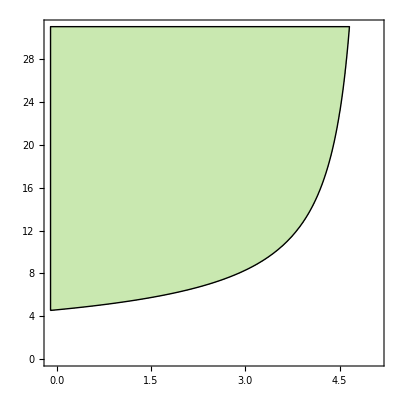
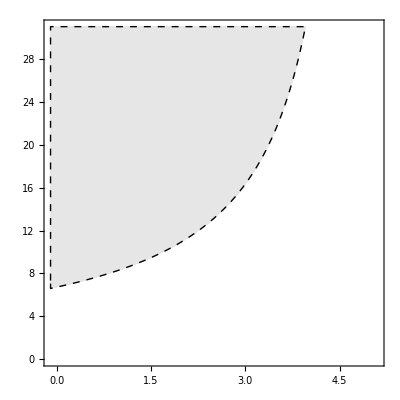
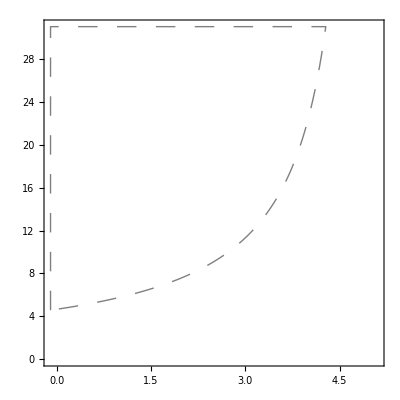
```mathematica
Persist=-Graphics-;Ant=-Graphics-;Ancestral=-Graphics-;
Show[Persist,Ant,ListPlot[{{5-2.527649751507285,7.823276823307988}},PlotStyle->{Black,PointSize[0.04]}],ListPlot[{{5-1.6,30}},PlotMarkers->{Graphics[{EdgeForm[{Black,Thick}],FaceForm[White],Disk[]}],0.04}],Ancestral,FrameStyle->Black,PlotRange->{{0.1,4.9},{0.6,30.2}},FrameTicks->{Automatic,Automatic,None,None},AspectRatio->1,LabelStyle->Directive[FontSize->20]]
```

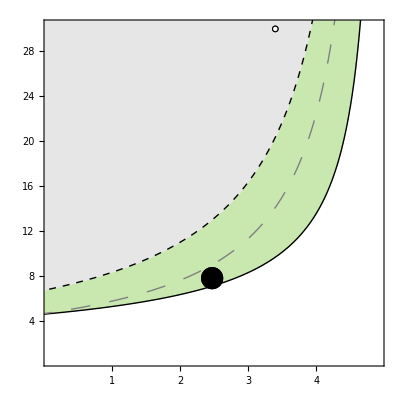

#### Plot ecological equilibria and evolutionary dynamics: Figure 2e,f

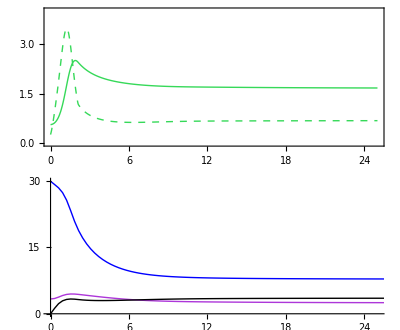

```mathematica
GraphicsGrid[{{Plot[{coex[[1,2]]/.evoParam/.vP->vP[T]/.hP->hP[T]/.bP->bP[T]/.vI->vI[T]/.hI->hI[T]/.eqsolEvo,coex[[2,2]]+coex[[3,2]]/.evoParam/.vP->vP[T]/.hP->hP[T]/.bP->bP[T]/.vI->vI[T]/.hI->hI[T]/.eqsolEvo},{T,0,25},PlotStyle->{{RGBColor[54/255,217/255,89/255],Thick},{RGBColor[54/255,217/255,89/255],Dashed,Thick}},PlotRange->{{0,25},{0,4}},Frame->True,FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},AspectRatio->0.4,LabelStyle->Directive[FontSize->12]]},{Plot[{vf/.evoParam/.vP->vP[T]/.hP->hP[T]/.bP->bP[T]/.vI->vI[T]/.hI->hI[T]/.eqsolEvo,hMax-hf/.evoParam/.vP->vP[T]/.hP->hP[T]/.bP->bP[T]/.vI->vI[T]/.hI->hI[T]/.eqsolEvo,bf/.evoParam/.vP->vP[T]/.hP->hP[T]/.bP->bP[T]/.vI->vI[T]/.hI->hI[T]/.eqsolEvo},{T,0,end},PlotRange->{{0,25},{0,30}},PlotStyle->{{Blue,Thick},{RGBColor[173/255,54/255,217/255],Thick},{Black,Thick}},TicksStyle->Black,AxesStyle->Black,AspectRatio->0.4,LabelStyle->Directive[FontSize->12]]}}]
```

### D. discolor with alternative nectar source (A. palmeri)

#### Simulate evolutionary dynamics

##### Note: The error “NDSolve: The function value ... is not a real number when the arguments are ... ” indicates evolutionary purging of the insect. The error occurs because the insect equilibrium becomes an imaginary number when it is extinct. To avoid evolutionary purging, try varying the value of cPV and/or cPH or increasing vMax Note: If host evolves zero defense, try increasing hMax Note: for the ancestral interaction, set bMax = 0, cB = 0, and cPV = 0

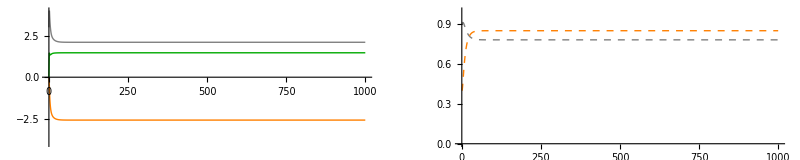

hP: 2.09951 vP: -2.57838 bP: 1.4676

hI: 0.780739 vI: 0.849296

v: 7.53522 h: 1.05512 b: 3.12692

e: 0.514053 Equilibrium: {P→1.6484,L→0.990075,A→0.0156697}

```mathematica
(* Parameters *)
(* Note: cB, cPH, cPV used instead of c^x_P,i as in manuscript *)
evoParam={vMax->50,hMax->5,bMax->5,eMax->1,H->0.1,ϵ->3,m->0.003,dL->0.3,dA->0.2,bS->1,vS->1,hS->1,cB->0.5,cPV->0.4,cPH->0.5,cIV->0.5,cIH->0.5};
end=1000; (* how long to run eco-evolutionary model *)

(* Evolutionary dynamics *)
Off[NDSolve::nrnum1]
Off[NDSolve::evcvmit]
Off[InterpolatingFunction::dmval]
dHPt=hP'[T]==-(cPH dA ⅇ^(cIH hI[T]^2+cIV vI[T]^2) (1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)) (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS))))/(hMax m vMax ϵ)+1/(2 hMax m vMax^2 ϵ)ⅇ^(cIH hI[T]^2+(-hI[T]+hP[T]) hS+cIV vI[T]^2) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2 hS (-(dA dL vMax)/(1+ⅇ^(-(vI[T]+vP[T]) vS))-(dA hMax m vMax)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-(dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) (-1+2/(1+ⅇ^(-bP[T] bS))) hMax m bMax vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+√(1/((1+ⅇ^(-(vI[T]+vP[T]) vS))^2)vMax^2 (-1/(1+ⅇ^((-hI[T]+hP[T]) hS))4 dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax ϵ (dA (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS)))-(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))))+((ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m (1+(-1+2/(1+ⅇ^(-bP[T] bS))) bMax) vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-dA (dL+(hMax (m+ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H ϵ))/(1+ⅇ^((-hI[T]+hP[T]) hS))))^2)));
dVPt=vP'[T]==-(cPV dA ⅇ^(cIH hI[T]^2+cIV vI[T]^2) (1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)) (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS))))/(hMax m vMax ϵ)-(ⅇ^(2 cIH hI[T]^2+2 cIV vI[T]^2-(vI[T]+vP[T]) vS) (1+ⅇ^((-hI[T]+hP[T]) hS))^2 (1+ⅇ^(-(vI[T]+vP[T]) vS)) (-1+2/(1+ⅇ^(-bP[T] bS))) bMax vS (-(dA dL vMax)/(1+ⅇ^(-(vI[T]+vP[T]) vS))-(dA hMax m vMax)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-(dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) (-1+2/(1+ⅇ^(-bP[T] bS))) hMax m bMax vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+√(1/((1+ⅇ^(-(vI[T]+vP[T]) vS))^2)vMax^2 (-1/(1+ⅇ^((-hI[T]+hP[T]) hS))4 dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax ϵ (dA (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS)))-(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))))+((ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m (1+(-1+2/(1+ⅇ^(-bP[T] bS))) bMax) vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-dA (dL+(hMax (m+ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H ϵ))/(1+ⅇ^((-hI[T]+hP[T]) hS))))^2)))^2)/(4 dA^2 hMax^2 vMax^2 ϵ^2 (H+1/(2 dA hMax vMax ϵ)ⅇ^(cIH hI[T]^2+cIV vI[T]^2) (1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)) (-(dA dL vMax)/(1+ⅇ^(-(vI[T]+vP[T]) vS))-(dA hMax m vMax)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-(dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) (-1+2/(1+ⅇ^(-bP[T] bS))) hMax m bMax vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+√(1/((1+ⅇ^(-(vI[T]+vP[T]) vS))^2)vMax^2 (-1/(1+ⅇ^((-hI[T]+hP[T]) hS))4 dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax ϵ (dA (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS)))-(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))))+((ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m (1+(-1+2/(1+ⅇ^(-bP[T] bS))) bMax) vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-dA (dL+(hMax (m+ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H ϵ))/(1+ⅇ^((-hI[T]+hP[T]) hS))))^2))))^2)+(ⅇ^(cIH hI[T]^2+cIV vI[T]^2-(vI[T]+vP[T]) vS) (1+ⅇ^((-hI[T]+hP[T]) hS)) (-1+2/(1+ⅇ^(-bP[T] bS))) bMax vS (-(dA dL vMax)/(1+ⅇ^(-(vI[T]+vP[T]) vS))-(dA hMax m vMax)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-(dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) (-1+2/(1+ⅇ^(-bP[T] bS))) hMax m bMax vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+√(1/((1+ⅇ^(-(vI[T]+vP[T]) vS))^2)vMax^2 (-1/(1+ⅇ^((-hI[T]+hP[T]) hS))4 dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax ϵ (dA (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS)))-(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))))+((ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m (1+(-1+2/(1+ⅇ^(-bP[T] bS))) bMax) vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-dA (dL+(hMax (m+ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H ϵ))/(1+ⅇ^((-hI[T]+hP[T]) hS))))^2))))/(2 dA hMax vMax ϵ (H+1/(2 dA hMax vMax ϵ)ⅇ^(cIH hI[T]^2+cIV vI[T]^2) (1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)) (-(dA dL vMax)/(1+ⅇ^(-(vI[T]+vP[T]) vS))-(dA hMax m vMax)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-(dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) (-1+2/(1+ⅇ^(-bP[T] bS))) hMax m bMax vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+√(1/((1+ⅇ^(-(vI[T]+vP[T]) vS))^2)vMax^2 (-1/(1+ⅇ^((-hI[T]+hP[T]) hS))4 dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax ϵ (dA (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS)))-(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))))+((ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m (1+(-1+2/(1+ⅇ^(-bP[T] bS))) bMax) vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-dA (dL+(hMax (m+ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H ϵ))/(1+ⅇ^((-hI[T]+hP[T]) hS))))^2)))));
dBt=bP'[T]==-(cB dA ⅇ^(cIH hI[T]^2+cIV vI[T]^2) (1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)) (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS))))/(hMax m vMax ϵ)+(ⅇ^(cIH hI[T]^2-bP[T] bS+cIV vI[T]^2) (1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)) bMax bS (-(dA dL vMax)/(1+ⅇ^(-(vI[T]+vP[T]) vS))-(dA hMax m vMax)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-(dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) (-1+2/(1+ⅇ^(-bP[T] bS))) hMax m bMax vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+√(1/((1+ⅇ^(-(vI[T]+vP[T]) vS))^2)vMax^2 (-1/(1+ⅇ^((-hI[T]+hP[T]) hS))4 dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax ϵ (dA (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS)))-(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))))+((ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m (1+(-1+2/(1+ⅇ^(-bP[T] bS))) bMax) vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-dA (dL+(hMax (m+ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H ϵ))/(1+ⅇ^((-hI[T]+hP[T]) hS))))^2))))/(dA (1+ⅇ^(-bP[T] bS))^2 hMax vMax ϵ (H+1/(2 dA hMax vMax ϵ)ⅇ^(cIH hI[T]^2+cIV vI[T]^2) (1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)) (-(dA dL vMax)/(1+ⅇ^(-(vI[T]+vP[T]) vS))-(dA hMax m vMax)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-(dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) (-1+2/(1+ⅇ^(-bP[T] bS))) hMax m bMax vMax^2 ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))^2)+√(1/((1+ⅇ^(-(vI[T]+vP[T]) vS))^2)vMax^2 (-1/(1+ⅇ^((-hI[T]+hP[T]) hS))4 dA ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H hMax ϵ (dA (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS)))-(ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS))))+((ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) hMax m (1+(-1+2/(1+ⅇ^(-bP[T] bS))) bMax) vMax ϵ)/((1+ⅇ^((-hI[T]+hP[T]) hS)) (1+ⅇ^(-(vI[T]+vP[T]) vS)))-dA (dL+(hMax (m+ⅇ^(-cIH hI[T]^2-cIV vI[T]^2) H ϵ))/(1+ⅇ^((-hI[T]+hP[T]) hS))))^2)))));
dHIt=hI'[T]==1/2 (-(ⅇ^((-hI[T]+hP[T]) hS) hMax hS m)/((1+ⅇ^((-hI[T]+hP[T]) hS))^2)+((2 ⅇ^((-hI[T]+hP[T]) hS) hMax hS m (dA+dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS))))/((1+ⅇ^((-hI[T]+hP[T]) hS))^2)-4 ((dA ⅇ^((-hI[T]+hP[T]) hS) hMax hS m)/((1+ⅇ^((-hI[T]+hP[T]) hS))^2)+2 cIH dA hI[T] (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS)))-(dA ⅇ^((-hI[T]+hP[T]) hS) hS (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS))))/(1+ⅇ^((-hI[T]+hP[T]) hS))))/(2 √((dA+dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS)))^2-4 (dA dL+(dA hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS))-dA (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS)))))));
dVIt=vI'[T]==-(2 cIV dA (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS))) vI[T]-(dA ⅇ^(-(vI[T]+vP[T]) vS) (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS))) vS)/(1+ⅇ^(-(vI[T]+vP[T]) vS)))/(√((dA+dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS)))^2-4 (dA dL+(dA hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS))-dA (dL+(hMax m)/(1+ⅇ^((-hI[T]+hP[T]) hS))))));
eqsolEvo=NDSolve[{dHPt/.evoParam,dVPt/.evoParam,dBt/.evoParam,dHIt/.evoParam,dVIt/.evoParam,hP[0]==3,vP[0]==0,bP[0]==0,hI[0]==0.9,vI[0]==0.4,WhenEvent[hP[T]<-0.0001,hP[T]->0],WhenEvent[Im[vP[T]]≠0,{"StopIntegration",end=T,Print["Plant purges insect"]}]},{hP,vP,bP,hI,vI},{T,0,end}];

(* Trait dynamics *)
GraphicsGrid[{{Plot[{hP[t]/.eqsolEvo,vP[t]/.eqsolEvo,bP[t]/.eqsolEvo},{t,0,end},PlotRange->{{0,end},{-4,4}},PlotStyle->{{Gray,Thick},{Orange,Thick},{Darker[Green],Thick}},AspectRatio->0.4,TicksStyle->Black,AxesStyle->Black,LabelStyle->Directive[FontSize->12]],
Plot[{hI[t]/.eqsolEvo,vI[t]/.eqsolEvo},{t,0,end},PlotRange->{{0,end},{0,1}},PlotStyle->{{Gray,Dashed,Thick},{Orange,Dashed,Thick}},AspectRatio->0.4,TicksStyle->Black,AxesStyle->Black,LabelStyle->Directive[FontSize->12]]}}]

(* Trait coESS *)
Print["hP: ",(hP[end]/.eqsolEvo[[1]])," vP: ",(vP[end]/.eqsolEvo)[[1]]," bP: ",(bP[end]/.eqsolEvo)[[1]]]
Print["hI: ",(hI[end]/.eqsolEvo)[[1]]," vI: ",(vI[end]/.eqsolEvo)[[1]]]

(* Trait functions *)
Print["v: ",(vf/.evoParam/.vP->vP[end]/.hP->hP[end]/.bP->bP[end]/.vI->vI[end]/.hI->hI[end]/.eqsolEvo)[[1]]," h: ",(hf/.evoParam/.vP->vP[end]/.hP->hP[end]/.bP->bP[end]/.vI->vI[end]/.hI->hI[end]/.eqsolEvo)[[1]]," b: ",(bf/.evoParam/.vP->vP[end]/.hP->hP[end]/.bP->bP[end]/.vI->vI[end]/.hI->hI[end]/.eqsolEvo)[[1]]]
Print["e: ",(ef/.evoParam/.vP->vP[end]/.hP->hP[end]/.bP->bP[end]/.vI->vI[end]/.hI->hI[end]/.eqsolEvo)[[1]],
" Equilibrium: ",(coex/.evoParam/.vP->vP[end]/.hP->hP[end]/.bP->bP[end]/.vI->vI[end]/.hI->hI[end]/.eqsolEvo)[[1]]]
```

#### Parameter Space: Figure 4d

NOTE: To simply create Figure 4d, please see section “Figure 4d” below.

```mathematica
(* Parameters: *)
plotParam={hMax->5,b->3.126923880756207,H->0.1,m->0.003,ϵ->3,e->0.5140533493438043,dL->0.3,dA->0.2};

(* Parameter space *)
Off[ParametricNDSolve::ndsz]
Off[ParametricNDSolve::nrnum1]
Off[InterpolatingFunction::dmvali]
Off[NIntegrate::inumr]
Off[NIntegrate::sLdcon]
Off[NIntegrate::ncvb]
Off[Greater::nord]
Off[NIntegrate::slwcon]
(* Ancestral M. sexta persists as pure herbivore *)
Ancestral=RegionPlot[{(ecoCoex[[3,2]]>0)/.h->hMax-x/.{hMax->5,b->0,H->0.1,m->0.003,ϵ->3,e->0.7,dL->0.3,dA->0.2}},{x,-0.1,5.1},{v,0,31},PlotStyle->Opacity[0],BoundaryStyle->{Gray,Dashing[Large],Thick},FrameStyle->Black,AspectRatio->1,LabelStyle->Directive[FontSize->20]]
(* M. sexta persists *)Persist=RegionPlot[(ecoCoex[[3,2]]>0)/.h->hMax-x/.plotParam,{x,-0.1,5.1},{v,0,31},PlotStyle->RGBColor[201/255,232/255,176/255],BoundaryStyle->{Black,Thick}]
(* Net Antagonism *)
NM=RegionPlot[{(ecoCoex[[1,2]]<1&&ecoCoex[[3,2]]>0)/.h->hMax-x/.plotParam},{x,-0.1,5.1},{v,0,31},PlotStyle->GrayLevel[0.9],BoundaryStyle->{Black,Dashed,Thick}]
```

#### Figure 4d

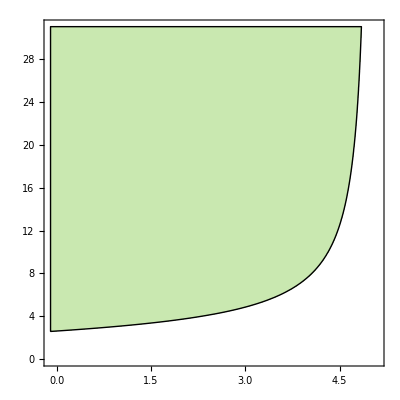
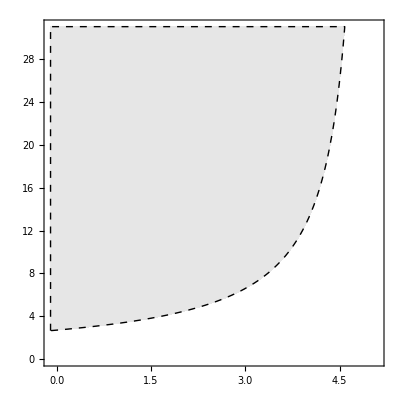
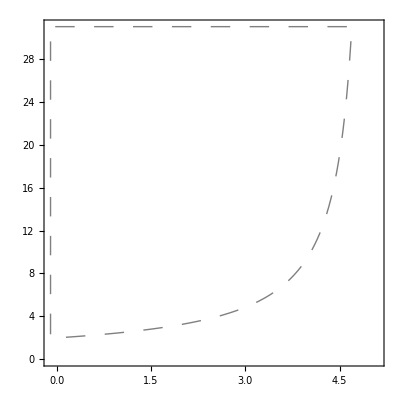
```mathematica
Persist=-Graphics-;Ant=-Graphics-;Ancestral=-Graphics-;
Show[Persist,Ant,ListPlot[{{5-1.0551163865693332,7.535219311315237}},PlotStyle->{Black,PointSize[0.04]}],ListPlot[{{5-0.6,30}},PlotMarkers->{Graphics[{EdgeForm[{Black,Thick}],FaceForm[White],Disk[]}],0.04}],Ancestral,FrameStyle->Black,PlotRange->{{0.1,4.9},{0.6,30.2}},FrameTicks->{Automatic,Automatic,None,None},AspectRatio->1,LabelStyle->Directive[FontSize->20]]
```

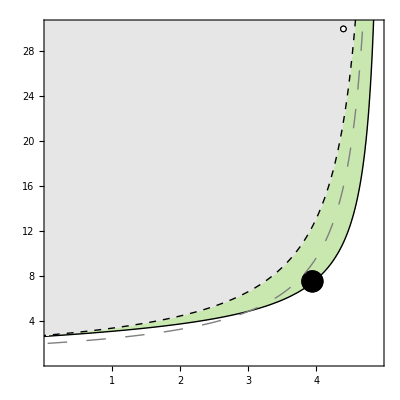

#### Plot ecological equilibria and evolutionary dynamics: Figure 4h,l

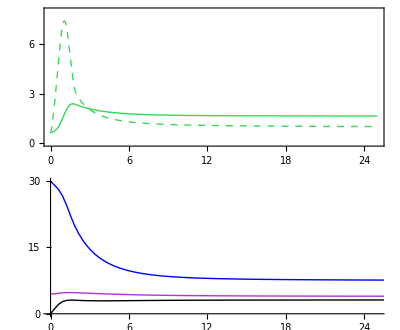

```mathematica
GraphicsGrid[{{Plot[{coex[[1,2]]/.evoParam/.vP->vP[T]/.hP->hP[T]/.bP->bP[T]/.vI->vI[T]/.hI->hI[T]/.eqsolEvo,coex[[2,2]]+coex[[3,2]]/.evoParam/.vP->vP[T]/.hP->hP[T]/.bP->bP[T]/.vI->vI[T]/.hI->hI[T]/.eqsolEvo},{T,0,25},PlotStyle->{{RGBColor[54/255,217/255,89/255],Thick},{RGBColor[54/255,217/255,89/255],Dashed,Thick}},PlotRange->{{0,25},{0,8}},Frame->True,FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},AspectRatio->0.4,LabelStyle->Directive[FontSize->12]]},{Plot[{vf/.evoParam/.vP->vP[T]/.hP->hP[T]/.bP->bP[T]/.vI->vI[T]/.hI->hI[T]/.eqsolEvo,hMax-hf/.evoParam/.vP->vP[T]/.hP->hP[T]/.bP->bP[T]/.vI->vI[T]/.hI->hI[T]/.eqsolEvo,bf/.evoParam/.vP->vP[T]/.hP->hP[T]/.bP->bP[T]/.vI->vI[T]/.hI->hI[T]/.eqsolEvo},{T,0,end},PlotRange->{{0,25},{0,30}},PlotStyle->{{Blue,Thick},{RGBColor[173/255,54/255,217/255],Thick},{Black,Thick}},TicksStyle->Black,AxesStyle->Black,AspectRatio->0.4,LabelStyle->Directive[FontSize->12]]}}]
```

#### Systematically vary insect costs for D. discolor: Figure 5b

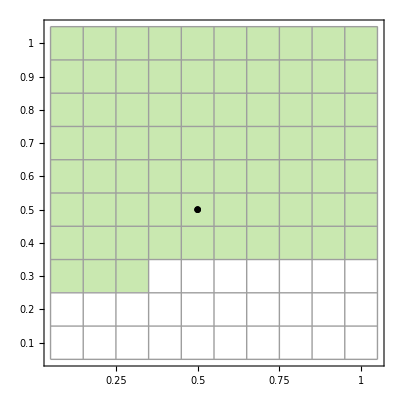

```mathematica
(* cIH from left-to-right, cIV from bottom-to-top *)
(* 0 = transition to mutualism, -1 = insect purged, 1 = antagonism *)
outcome={{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}};

(* Plot *)
Show[MatrixPlot[Reverse[outcome],AspectRatio->1,ColorRules->{-1->White,0->RGBColor[201/255,232/255,176/255],1->Gray},DataReversed->True,FrameStyle->Black,LabelStyle->Directive[FontSize->20],Mesh->True,FrameTicks->{{{{1,0.1},{2,0.2},{3,0.3},{4,0.4},{5,0.5},{6,0.6},{7,0.7},{8,0.8},{9,0.9},{10,1}},None},{{{0,0},{2.5,0.25},{5,0.5},{7.5,0.75},{10,1}},None}}],
ListPlot[{{9 0.5,9 0.5}},PlotMarkers->{Graphics[{EdgeForm[{Black,Thick}],FaceForm[Black],Disk[]}],0.05}]]
```

#### Systematically vary plant costs for D. discolor: Figure 5d

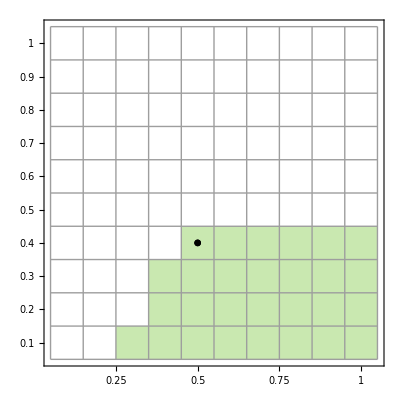

```mathematica
(* cPH from left-to-right, cPV from bottom-to-top *)
(* 0 = transition to mutualism, -1 = insect purged, 1 = antagonism *)
outcome={{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},
{-1,-1,-1,-1,0,0,0,0,0,0},
{-1,-1,-1,0,0,0,0,0,0,0},
{-1,-1,-1,0,0,0,0,0,0,0},
{-1,-1,0,0,0,0,0,0,0,0}};

(* Plot *)
Show[MatrixPlot[Reverse[outcome],AspectRatio->1,ColorRules->{-1->White,0->RGBColor[201/255,232/255,176/255],1->Gray},DataReversed->True,FrameStyle->Black,LabelStyle->Directive[FontSize->20],Mesh->True,FrameTicks->{{{{1,0.1},{2,0.2},{3,0.3},{4,0.4},{5,0.5},{6,0.6},{7,0.7},{8,0.8},{9,0.9},{10,1}},None},{{{0,0},{2.5,0.25},{5,0.5},{7.5,0.75},{10,1}},None}}],
ListPlot[{{9 0.5,7 0.5}},PlotMarkers->{Graphics[{EdgeForm[{Black,Thick}],FaceForm[Black],Disk[]}],0.05}]]
```